```mathematica
(*Change of variables from FHN1 -> FHN2*)
maxtime=100;
ep=0.08;β=0.7;γ=0.8;δ=1;d1 =1; d2=0;(*Ratas*)
(*ep=0.08;β=0.8;γ=0.5;δ=1;d1 =1; d2=0;*)(*Weinberg*)
eqn= FindRoot[δ v-v^3/3-(v+β)/γ==0,{v,-1}];
{v0,w0}={v,(v+β)/γ}/.eqn;
A=(3v0+Sqrt[12 δ-3v0^2])/(6δ-6v0^2);
B=3A^3;
K1=3A^2;
K2=Sqrt[K1];
τ=1/(9 ep A^4);
α=-3 A v0 -1;
γt=γ Sqrt[ep τ];Print["\\gamma = ",γ,", \\quad \\beta = ",β, ", \\quad \\varepsilon = ", ep,", \\quad v_0 = ",v0,", \\quad w_0= ",w0,","]
Print["\\tau = ",τ,", \\quad \\alpha = ",α,", \\quad \\tilde{\\gamma} = ",γt,","]
Print["A= ",A,", \\quad B = ",B, ", \\quad K_1 = ",K1, ", \\quad K_2 = ",K2,","]
```

\gamma = 0.8, \quad \beta = 0.7, \quad \varepsilon = 0.08, \quad v_0 = -1.19941, \quad w_0= -0.62426,

\tau = 142.949, \quad \alpha = 0.129692, \quad \tilde{\gamma} = 2.70536,

A= 0.313958, \quad B = 0.0928404, \quad K_1 = 0.295709, \quad K_2 = 0.543792,

{InterpolatingFunction[…],InterpolatingFunction[…]}

{InterpolatingFunction[…],InterpolatingFunction[…]}

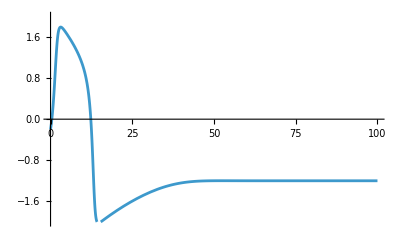

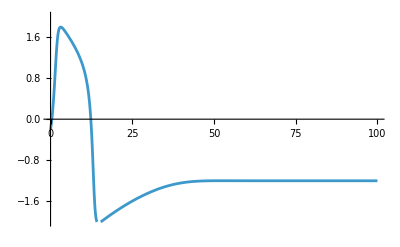

```mathematica
(*Comparison Simulation*)
{V1,W1}=NDSolveValue[{v'[t]==δ v[t]-v[t]^3/3-w[t],w'[t]==ep(v[t]-γ w[t] + β),v[0]==v0+1,w[0]==w0},{v,w},{t,0,maxtime}]
{X1,Y1}=NDSolveValue[{x'[t]==x[t](1-x[t])(x[t]-α)-y[t],τ y'[t]==x[t]-γt y[t],x[0]==A(V1[0]-v0),y[0]==B (W1[0]-w0)},{x,y},{t,0,maxtime/K1}]
Plot[V1[t],{t,0,maxtime},PlotRange->{-2,2}]
Plot[v0+(1/A)X1[t/K1],{t,0,maxtime},PlotRange->{-2,2}]
```